```mathematica
Parallelize[Abs[{1,0,1}-{2,3,4}]/{2,3,4}]
```

{1/2,1,3/4}

```mathematica
Sum[(((-1)^m)/(m!*(m+3)!)) 1/(2 π^2 r (2+√(a^2+r^2-2 a r t) u)^3)a √(a^2+r^2-2 a r t) (2/(√(a^2+r^2-2 a r t))+u)^3 (a √((2 √(a^2+r^2-2 a r t)+a^2 u+r^2 u-2 a r t u)/(a^2+r^2-2 a r t)))^(2 m) ((4 (2 √(a^2+r^2-2 a r t)+a^2 u+r^2 u-2 a r t u))/(1+m)+(6 (a^2+r^2-2 a r t)^(3/2) u^2 (1+1/2 √(a^2+r^2-2 a r t) u)^-m Hypergeometric2F1[1-m,-m,2-m,-1/2 √(a^2+r^2-2 a r t) u])/(-1+m)+((a^2+r^2-2 a r t)^2 u^3 (1+1/2 √(a^2+r^2-2 a r t) u)^-m Hypergeometric2F1[2-m,-m,3-m,-1/2 √(a^2+r^2-2 a r t) u])/(-2+m)+(12 (a^2+r^2-2 a r t) u (1+1/2 √(a^2+r^2-2 a r t) u)^-m Hypergeometric2F1[-m,-m,1-m,-1/2 √(a^2+r^2-2 a r t) u])/m),{m,0,Infinity}]
```

∑_(m=0)^∞ 1/(2 π^2 r (2+√(a^2+r^2-2 a r t) u)^3 m! (3+m)!)(-1)^m a √(a^2+r^2-2 a r t) (2/(√(a^2+r^2-2 a r t))+u)^3 (a √((2 √(a^2+r^2-2 a r t)+a^2 u+r^2 u-2 a r t u)/(a^2+r^2-2 a r t)))^(2 m) ((4 (2 √(a^2+r^2-2 a r t)+a^2 u+r^2 u-2 a r t u))/(1+m)+(6 (a^2+r^2-2 a r t)^(3/2) u^2 (1+1/2 √(a^2+r^2-2 a r t) u)^-m Hypergeometric2F1[1-m,-m,2-m,-1/2 √(a^2+r^2-2 a r t) u])/(-1+m)+((a^2+r^2-2 a r t)^2 u^3 (1+1/2 √(a^2+r^2-2 a r t) u)^-m Hypergeometric2F1[2-m,-m,3-m,-1/2 √(a^2+r^2-2 a r t) u])/(-2+m)+(12 (a^2+r^2-2 a r t) u (1+1/2 √(a^2+r^2-2 a r t) u)^-m Hypergeometric2F1[-m,-m,1-m,-1/2 √(a^2+r^2-2 a r t) u])/m)

```mathematica
∫_-1^1 ((√(2/(√(a^2-2 a r t+r^2))-0.0827625))^3 HeavisideTheta[2/(√(a^2-2 r t a+r^2))-0.0827625] BesselJ[3,2 a √(2/(√(a^2-2 r t a+r^2))-0.0827625)])/(2 π^2 a)ⅆt
```

∫_-1^1 ((-0.0827625+2/(√(a^2+r^2-2 a r t)))^(3/2) BesselJ[3,2 a √(-0.0827625+2/(√(a^2+r^2-2 a r t)))] HeavisideTheta[-0.0827625+2/(√(a^2+r^2-2 a r t))])/(2 a π^2)ⅆt

```mathematica
Simplify[∫_-1^1 ((-0.0827625+2/(√(a^2+r^2-2 a r t)))^(3/2) BesselJ[3,2 a √(-0.0827625+2/(√(a^2+r^2-2 a r t)))] HeavisideTheta[-0.0827625+2/(√(a^2+r^2-2 a r t))])/(2 a π^2)ⅆt]
```

∫_-1^1 1/(2 a π^2)(-0.0827625+2/(√(a^2+r^2-2 a r t)))^(3/2) BesselJ[3,2 a √(-0.0827625+2/(√(a^2+r^2-2 a r t)))] HeavisideTheta[-0.0827625+2/(√(a^2+r^2-2 a r t))]ⅆt

```mathematica
T[t_,r_,a_]=√(u+2/(√(a^2+r^2-2 a r t)))
```

√(2/(√(a^2+r^2-2 a r t))+u)

```mathematica
InverseFunction[Function[{r},√(2/(√(a^2+r^2-2 a r t))+u)]][r]
```

```mathematica
Subscript[T, x][x_]=((a^2)+(r^2)-(2/(-u+x^2)^2))/(2a r)
```

(a^2+r^2-2/((-u+x^2)^2))/(2 a r)

```mathematica
D[(a^2+r^2-2/((-u+x^2)^2))/(2 a r), x]
```

(4 x)/(a r (-u+x^2)^3)

(3 √(2/(√(a^2+r^2-2 a r t))+u) BesselJ[4,√(2/(√(a^2+r^2-2 a r t))+u)])/((a^2+r^2-2 a r t)^(3/2))+((2/(√(a^2+r^2-2 a r t))+u) (BesselJ[3,√(2/(√(a^2+r^2-2 a r t))+u)]-BesselJ[5,√(2/(√(a^2+r^2-2 a r t))+u)]))/(2 (a^2+r^2-2 a r t)^(3/2))

```mathematica
Integrate[(((a √(2/(√(a^2+r^2-2 a r t))+u))^(3+2m))*(2a √(2/(√(a^2+r^2-2 a r t))+u))^3)/(16a^4 Pi^2),t]
```

1/(2 π^2 r (2+√(a^2+r^2-2 a r t) u)^3)a √(a^2+r^2-2 a r t) (2/(√(a^2+r^2-2 a r t))+u)^3 (a √((2 √(a^2+r^2-2 a r t)+a^2 u+r^2 u-2 a r t u)/(a^2+r^2-2 a r t)))^(2 m) ((4 (2 √(a^2+r^2-2 a r t)+a^2 u+r^2 u-2 a r t u))/(1+m)+(6 (a^2+r^2-2 a r t)^(3/2) u^2 (1+1/2 √(a^2+r^2-2 a r t) u)^-m Hypergeometric2F1[1-m,-m,2-m,-1/2 √(a^2+r^2-2 a r t) u])/(-1+m)+((a^2+r^2-2 a r t)^2 u^3 (1+1/2 √(a^2+r^2-2 a r t) u)^-m Hypergeometric2F1[2-m,-m,3-m,-1/2 √(a^2+r^2-2 a r t) u])/(-2+m)+(12 (a^2+r^2-2 a r t) u (1+1/2 √(a^2+r^2-2 a r t) u)^-m Hypergeometric2F1[-m,-m,1-m,-1/2 √(a^2+r^2-2 a r t) u])/m)

```mathematica
D[x^4*BesselJ[4,x],x]
```

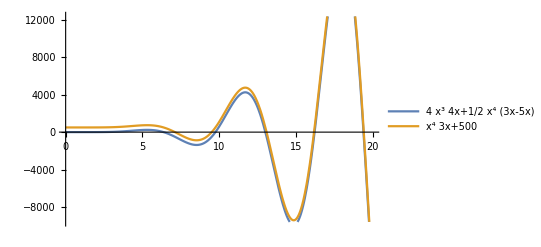

```mathematica
Plot[{4 x^3 BesselJ[4,x]+1/2 x^4 (BesselJ[3,x]-BesselJ[5,x]),x^4*BesselJ[3,x]+500},{x,0,20},PlotLegends->"Expressions"]
```